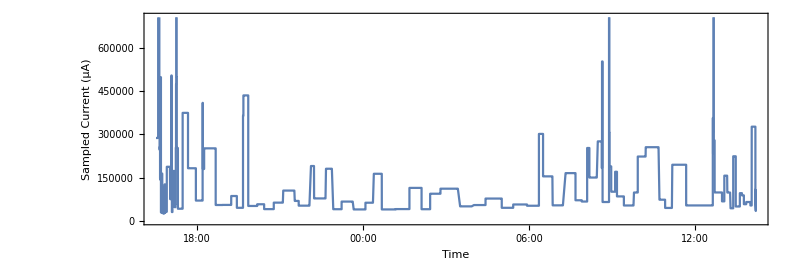

```mathematica
SetDirectory[NotebookDirectory[]];

raw =Import["!grep -B 15 'POWER_SUPPLY_CURRENT_NOW' ../Logs/2016-02-03-14-15-47.txt", "List"];
rawGrouped = Partition[raw, 17];
datesAndCurrentsMicroamps= {DateObject[#[[1]]], ToExpression[StringSplit[#[[16]], "="][[2]]]}&/@rawGrouped;
datesAndDischargeCurrentsMicroamps = Select[datesAndCurrentsMicroamps, #[[2]]≤ 0&];
datesAndDischargeCurrentsAbsoluteMicroamps = {#[[1]], Abs[#[[2]]]}&/@ datesAndDischargeCurrentsMicroamps;

DateListPlot[datesAndDischargeCurrentsAbsoluteMicroamps,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Current (μA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}]
```